# simple focal shift estimate using gaussian optics and linear optics

## 1/q=1/(R(z))-i λ0/(πnw(z))^2

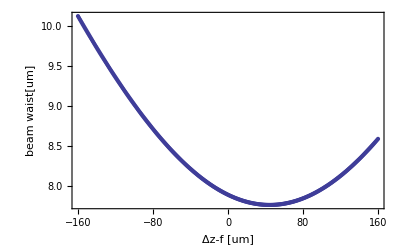

```mathematica
Clear["Global`*"]
kHz=10^3;
nm=10^-9;
mm=10^-3;
um=10^-6;
cm=10^-2;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λ=775nm;
n=1;

R = z(1+((π w0^2)/(λ z))^2);
w=w0 √(1+((λ z)/(π w0^2))^2);
f=16mm;
w0=1000um/2; (*approx*)
z=20cm; (*approx distance from fiber collimator to objective*)
q1= 1/(1/R-(I λ)/(π w^2)); (*q beam param of input AT the lens*)
q2=1/(1/q1-1/f);(*right after lens*)
dat= Reap[
Do[
q3=q2+Δz; (*after propagating some distance Δz*)

w=√(-λ/(π n Im[1/q3]));(*get waist*)
Sow[{(Δz-f)/um,w/um}]
,{Δz,.99f,1.01f,.001mm}]
][[2,1]];
ListPlot[dat,Axes->False,Frame->True,FrameLabel->{"Δz-f [um]","beam waist[um]"}]
```

simple ray optics estimate of deviation from focus 
from http : // www.newport.com/Focusing - and - Collimating/141191/1033/content.aspx

```mathematica
w0=1200um/2; (*estimate of input waist*)
f=16mm;
θ1= .5 10^-3; (*measured divergence angle*)

θ2=w0/f;
Δz=1. w0/Tan[θ2]-f;(*distance of projected waist from focus*)
Δz/um
```

-7.5007